16.1429

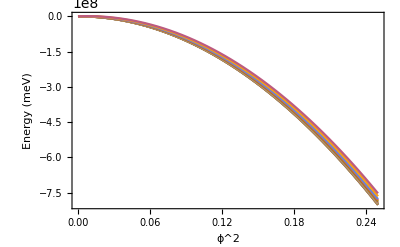

```mathematica
(*Constants*)
e = 1.602*10^(-19);
ℏ = 6.582*10^(-16);
hw = 0.191;
c = 2.998*10^8;
m0 = 0.51*10^6 / c^2;
m = 0.067*m0;
a = 0.56*10^(-9);
a = 1*10^(-9);
m = ℏ^2 / (2*10000*a^2);
K = hw / (ℏ*c);
Ef = 1*10^9;
phimax = Ef *a/hw;
phimax = 0.5;
B= K^2 *ℏ^3 * x / (m * a^2 *hw);
BMax= K^2 *ℏ^3 * phimax^2 / (m * a^2 *hw)
U = K * ℏ^3 * x / (2 * m * a^2 * hw);
w[n_] := 10^3((n+0.5)*ℏ*B/m - U^2/(4*m));
Plot[{w[0],w[1], w[2], w[3], w[4], w[5], w[10], w[15], w[20], w[30], w[40], w[50], w[75], w[100]}, {x,0,phimax^2}, Frame->True, FrameLabel->{"ϕ^2", "Energy (meV)", "",""}]
```